```mathematica
Clear["Global`*"]
```

```mathematica
R={r,θ,ϕ};
X={x,y,z};
RealSphericalHarmonicY[l_,m_,θ_,ϕ_]:=If[m<0,
ⅉ/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]-(-1)^m SphericalHarmonicY[l,-m,θ,ϕ]),
If[m==0,
SphericalHarmonicY[l,m,θ,ϕ],
1/Sqrt[2](SphericalHarmonicY[l,m,θ,ϕ]+(-1)^m SphericalHarmonicY[l,-m,θ,ϕ])
]
]
ψ[l_,m_]:=SphericalHankelH2[l,k r]RealSphericalHarmonicY[l,m,θ,ϕ]
Y[l_,m_]:=Grad[ψ[l,m],R,"Spherical"]
Ψ[l_,m_]:=1/k Curl[Φ[l,m],R,"Spherical"]
Φ[l_,m_]:=Curl[{r ψ[l,m],0,0},R,"Spherical"]
SphericalCrossProduct[a_,b_]:=Det@{{er,eθ,eϕ},a,b}/.{er->{1,0,0},eθ->{0,1,0},eϕ->{0,0,1}}
ElectricField[l_,m_,{radial_,polar_,azimuthal_}]:=(radial Y[l,m]+polar Ψ[l,m]+azimuthal Φ[l,m])
vec[l_,m_]:=Simplify[TransformedField["Spherical"->"Cartesian",Ψ[l,m],R->{x,y,z}]/.{
SphericalHankelH2[l1_,x_]:>1,
x->r Cos[ϕ]Sin[θ],
y->r Sin[ϕ]Sin[θ],
z->r Cos[θ],
k->1
}/.r->1,Assumptions->θ∈Reals&&θ>=0&&θ<=π]//N;
l0=4;m0=4;
res=ParallelTable[{l,m,NIntegrate[
RealSphericalHarmonicY[l,m,θ,ϕ] vec[l0,m0]Sin[θ],{θ,0,π},{ϕ,0,2π},
AccuracyGoal->3(*,MinRecursion->5*),Method->"GaussKronrodRule"
]},{l,0,4},{m,-l,l},Method->"EvaluationsPerKernel" -> 1];
Map[If[Abs@#<1*^-8,0,#]&,res,{-1}]
```

{{{0,0,{0,0,0}}},{{1,-1,{0,0,0}},{1,0,{0,0,0}},{1,1,{0,0,0}}},{{2,-2,{0,0,0}},{2,-1,{0,0,0}},{2,0,{0,0,0}},{2,1,{0,0,0}},{2,2,{0,0,0}}},{{3,-3,{0,-10.6066+3.30848×10^-16 ⅈ,0}},{3,-2,{0,0,0}},{3,-1,{0,0,0}},{3,0,{0,0,0}},{3,1,{0,0,0}},{3,2,{0,0,0}},{3,3,{-10.6066+1.2226×10^-16 ⅈ,0,0}}},{{4,-4,{0,0,0}},{4,-3,{0,0,0}},{4,-2,{0,0,0}},{4,-1,{0,0,0}},{4,0,{0,0,0}},{4,1,{0,0,0}},{4,2,{0,0,0}},{4,3,{0,0,0}},{4,4,{0,0,0}}}}

```mathematica
$Assumptions=$Assumptions&&θ∈Reals&&θ>0&&θ<π&&r∈Reals&&r>0&&ϕ∈Reals&&ϕ>0
```

θ∈ℝ&&θ>0&&θ<π&&r∈ℝ&&r>0&&ϕ∈ℝ&&ϕ>0

```mathematica
formula[l_,m_]:=Simplify[Simplify[
N@FunctionExpand@ExpToTrig@Sqrt[Total[Abs[GetDirectivity[l,m]]^2]/.{k->1,r->1}]
]/. x_/;Abs[x]<10^-7->0]
formula[4,4]
```

Sin[θ]^6 √(39.2719 Cos[θ]^4 Cos[(4.+0. ⅈ) ϕ]^4+78.5437 Cos[θ]^2 Cos[(4.+0. ⅈ) ϕ]^2 Sin[(4.+0. ⅈ) ϕ]^2+39.2719 Sin[(4.+0. ⅈ) ϕ]^4)

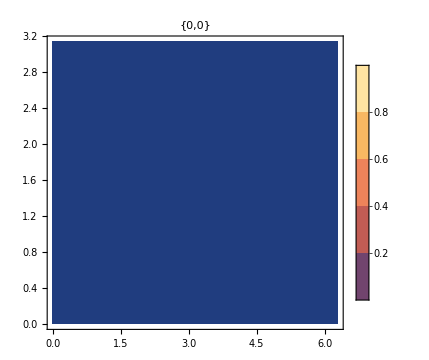
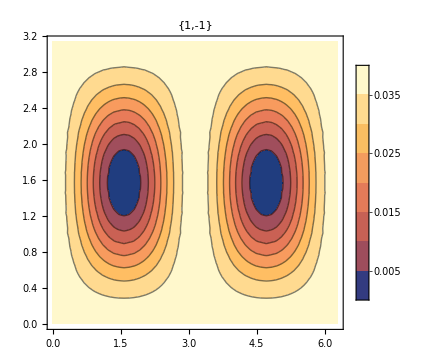
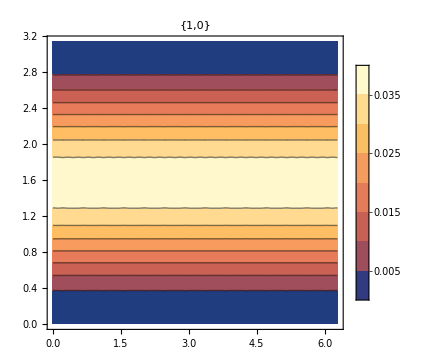
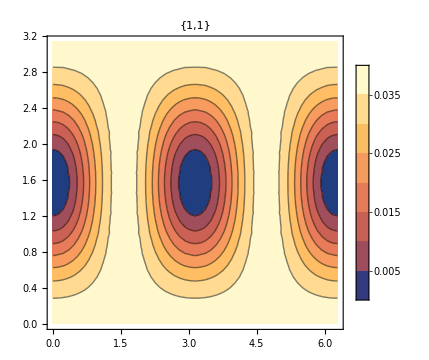

```mathematica
GetDirectivity[l_,m_]:=Module[{eField,bField,poynting,fom},
eField=ElectricField[l,m,{0,0,1}];
bField=1/(ⅉ)Curl[eField,R,"Spherical"];
poynting=Re@SphericalCrossProduct[eField,Conjugate@bField];
poynting
]
PlotDirectivity[poynting_,l_,m_]:=Module[{fom},
fom=Norm[poynting/.{k->2π,r->1}](*,Assumptions->θ∈Reals&&ϕ∈Reals*);
ContourPlot[fom,{ϕ,0,2π},{θ,0,π},PlotLabel->{l,m},PlotLegends->Automatic,ImageSize->Medium,MaxRecursion->2]
]
ParallelTable[Module[{p},
p=GetDirectivity[l,m];
PlotDirectivity[p,l,m]],
{l,0,1},{m,-l,l},Method->"CoarsestGrained"]
```